```mathematica
equ={θ''[t]+Sin[θ[t]]==0,θ[0]==0,θ'[0]==ω0};
Do[
s=NDSolve[equ,θ,{t,0,10}];
Plot[θ[t]/.s[[1]],{t,0,10},PlotRange->π/2],
{ω0,0,1,0.1}]
Clear[equ,s]
```

```mathematica
equ={θ''[t]+Sin[θ[t]]==0,θ[0]==0,θ'[0]==ω0};
Do[
s=NDSolve[equ,θ,{t,0,10}];
g=Plot[θ[t]/.s[[1]],{t,0,10},PlotRange->π/2];
Print[g],{ω0,0,1,0.1}]
Clear[equ,s,g]
```

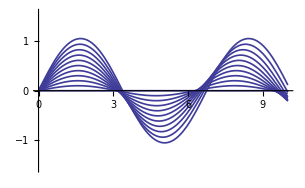

```mathematica
figure={};
equ={θ''[t]+Sin[θ[t]]==0,θ[0]==0,θ'[0]==ω0};
Do[
s=NDSolve[equ,θ,{t,0,10}];
g=Plot[θ[t]/.s[[1]],{t,0,10},PlotRange->π/2,
PlotStyle->Thickness[0.004]];
AppendTo[figure,g],{ω0,0,1,0.1}]
Show[figure,AxesStyle->Thickness[0.003]]
Clear[equ,s,g,figure]
```

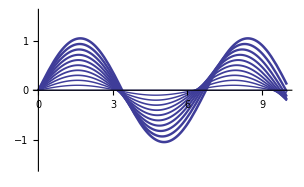

```mathematica
figure={};
equ={θ''[t]+Sin[θ[t]]==0,θ[0]==0,θ'[0]==ω0};
Do[
s=NDSolve[equ,θ,{t,0,10}];
g=Plot[θ[t]/.s[[1]],{t,0,10},PlotRange->π/2,
PlotStyle->Thickness[0.003+0.003×ω0]];
AppendTo[figure,g],{ω0,0,1,0.1}]
Show[figure,AxesStyle->Thickness[0.003]]
Clear[equ,s,g,figure]
```

```mathematica
t1={504.6,0.5173,505.6,0.8836,506.2,2.435,
506.3,3.462,506.4,5.236,506.5,9.615,506.6,
5.493,506.7,3.822,506.8,2.554,506.9,2.308,
507.0,1.816,507.8,0.6205,508.8,0.3803};
t2={505.3,4.51,505.6,6.275,506,10.75,506.3,
16.92,506.4,34.26,506.6,63.93,506.8,27.105,
507.0,18.045,507.2,10.425,507.5,7.68,508,
4.65,508.6,3.75};
```

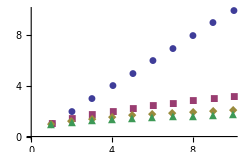

```mathematica
ListPlot[Table[n^(1/p),{p,4},{n,10}],
PlotMarkers->Automatic,AxesOrigin->{0,0},
AxesStyle->Thickness[0.003]]
```

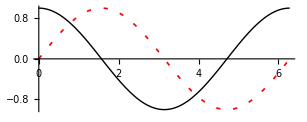

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2π},PlotStyle->
{{Red,Dashing[{0.01,0.03}],Thickness[0.004]},
Black},AxesStyle->Thick,AspectRatio->0.4]
```

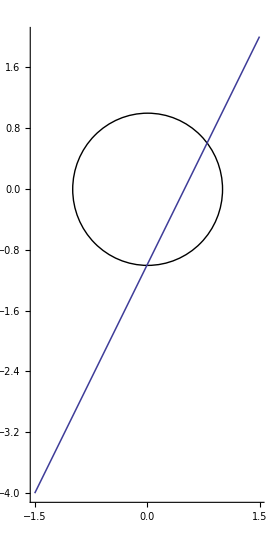

```mathematica
g1=Graphics[{Thick,Circle[]}];
g2=Plot[2x-1,{x,-1.5,1.5},
PlotStyle->Thickness[0.004]];
Show[{g1,g2},Axes->True,AspectRatio->Automatic,
AxesStyle->Thickness[0.003],PlotRange->1.5]
```

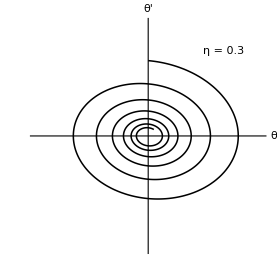

```mathematica
g=9.8;L=1.5;Ω=√(g/L);η=0.3;
v0=0.2;ω0=v0/L;tm=15;
s=NDSolve[{θ''[t]+Ω^2 Sin[θ[t]]+η θ'[t]==0,
θ[0]==0,θ'[0]==ω0},θ,{t,0,tm}];
θ=θ/.s[[1]];  
ParametricPlot[{θ[t],θ'[t]},{t,0,tm},
PlotRange->{{-0.06,0.06},{-0.2,0.2}},
AxesLabel->{"θ","θ'"},AspectRatio->1,
PlotStyle->{Thickness[0.004],Black},
AxesStyle->Thickness[0.003],Ticks->None,
Epilog->Text["η = "<>ToString[η],{0.04,0.15}],
BaseStyle->{FontSize->12}]
Clear[g,L,Ω,v0,ω0,η,tm,s,θ]
```

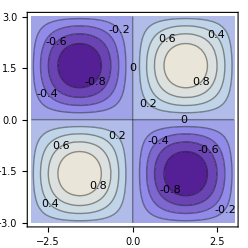

```mathematica
ContourPlot[Sin[x]Sin[y],{x,-3,3},{y,-3,3},
ContourLabels->True]
```

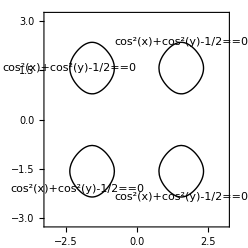

```mathematica
ContourPlot[Cos[x]^2+Cos[y]^2-1/2==0,{x,-π,π},
{y,-π,π},ContourLabels->True,
ContourStyle->Thick]
```

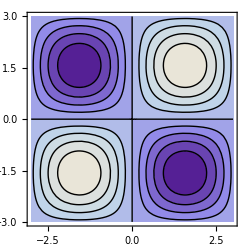

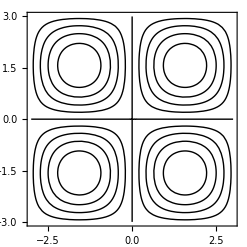

```mathematica
ContourPlot[Sin[x]Sin[y],{x,-3,3},{y,-3,3},
ContourStyle->Thick]
ContourPlot[Sin[x]Sin[y],{x,-3,3},{y,-3,3},
ContourShading->None,ContourStyle->Thick]
```

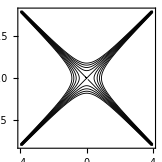

```mathematica
ContourPlot[x^2-y^2,{x,-4,4},
{y,-4,4},PlotRange->1,
ContourStyle->Thickness[0.004],
ContourShading->None]
```

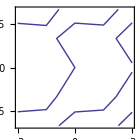
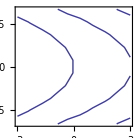
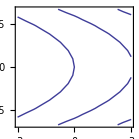
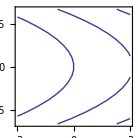

```mathematica
Table[ContourPlot[Sin[x+y^2]==0,{x,-3,3},
{y,-2,2},Mesh->None, MaxRecursion->0,
PlotPoints->pp,Axes->True],
{pp,{5,10,15,20}}]
```

```mathematica
Off[NIntegrate::"slwcon",NIntegrate::"ncvb"]
Do[
g=NIntegrate[1/Sqrt[Sin[x]],{x,0,10},
MaxRecursion->i];Print["i = ",i,",  g = ",g],
{i,2,60,5}]
```

i = 2,  g = 14.9402-8.55009 ⅈ

i = 7,  g = 10.1251-6.7483 ⅈ

i = 12,  g = 10.4677-6.75039 ⅈ

i = 17,  g = 10.4834-6.77007 ⅈ

i = 22,  g = 10.4869-6.76906 ⅈ

i = 27,  g = 10.4881-6.76922 ⅈ

i = 32,  g = 10.4882-6.76946 ⅈ

i = 37,  g = 10.4882-6.76947 ⅈ

i = 42,  g = 10.4882-6.76946 ⅈ

i = 47,  g = 10.4882-6.76947 ⅈ

i = 52,  g = 10.4882-6.76947 ⅈ

i = 57,  g = 10.4882-6.76947 ⅈ

```mathematica
NIntegrate[1/Sqrt[Sin[x]],
{x,0,π,2 π,3 π,10}]
```

10.4882-6.76947 ⅈ

```mathematica
Off[NIntegrate::"slwcon",NIntegrate::"ncvb"]
Do[g=NIntegrate[1/Sqrt[Sin[x]],
{x,0,10},WorkingPrecision->i];
Print["i = ",i,",  g = ",g],
{i,20,60,10}]
```

```mathematica
NDSolve[{{y1'[t]==y2[t], y1[0]==0}, {y2'[t]==-Ω^2 Sin[y1[t]], y2[0]==ω0}},
{y1,y2},{t,0,10}]
```

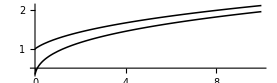

```mathematica
n=100;vars=Table[Subscript[x, i][t],{i,n}];
equs=Table[j=Mod[i,n]+1;
{Subscript[x, i]'[t]==1/(Subscript[x, i][t]+Subscript[x, j][t])^2,Subscript[x, i][0]==1/i},
{i,n}];
s=NDSolve[equs,{Subscript[x, 1],Subscript[x, 3]},{t,0,10}, 
DependentVariables->vars];
Plot[{Subscript[x, 1][t],Subscript[x, 3][t]}/.s[[1]],{t,0,10},
PlotStyle->{Thickness[0.004],Black},
AxesStyle->Thickness[0.003],
AspectRatio->0.3]
Clear[n,vars,equs,s]
```